```mathematica
Needs["NoisyQuantumTeleportationBenchmarking`", FileNameJoin[{NotebookDirectory[],"NoisyQuantumTeleportationBenchmarking.wl"}]]
```

```mathematica
ResourceFunction["MaTeXInstall"][];
<<MaTeX`
```

```mathematica
MaTeX["p_a"]
```

-Graphics-

```mathematica
latexStyle = {FontFamily ->  "LM Roman 12"};
```

```mathematica
contours = Association[{}];
```

```mathematica
newStyle[x_]:=x/. l_Line:>Sequence[Opacity[.4],Thick,Dashed,Red,l];
```

```mathematica
ForAllChannelsAndDistances[Function[{chA, chB, d, AvgDist}, 
th = GetDistanceThreshold[d];
(*Export["./contours/contour-"<> GetChannelOutputFantasyName[chA] <> "-" <> GetChannelOutputFantasyName[chB] <> "-" <> GetDistanceOutputFantasyName[d] <> ".png", plot*)
plot = ContourPlot[AvgDist[pA, pB],{pA,0,1},{pB,0,1},
AxesLabel->{Subscript[p, a], Subscript[p, b]}, Axes -> True, Frame->False,
Contours->(Sort[Append[FindDivisions[{#1,#2},#3], th]]&),
ContourLabels->All,
ColorFunction->(p|-> If[QuantumCertified[d, p], ColorData["HTML","LightCoral"], ColorData["HTML","CornflowerBlue"]]),
ColorFunctionScaling->False,MaxRecursion->3,Mesh->None,
PlotLabel->"Alice: "<>GetChannelLabel[chA]<>"\nBob: "<>GetChannelLabel[chB]<>"\nDistancia: "<>GetDistanceLabel[d]
]/. Tooltip[x_,th]:>Tooltip[newStyle[x],th];

AssociateTo[contours,{chA, chB, d} -> plot];
]]
```

```mathematica
plots=Partition[(Show[#, ImageSize -> 200, PlotLabel-> None, AxesLabel->{MaTeX["p_a"], MaTeX["p_b"]}, BaseStyle -> latexStyle])& /@ Values[contours], 4];
```

```mathematica
labelColumnas  = Prepend[MaTeX["\\text{"<>#<>"}"]&/@GetDistanceLabel/@Distances, ""];
labelFilas = MaTeX["\\text{"<>#<>"}"]&/@Flatten[Table["A: "<>GetChannelOutputFantasyName[chA]<>"\nB: "<>GetChannelOutputFantasyName[chB], {chA, Channels}, {chB, Channels}]];
```

```mathematica
(*Do[Print[Grid[{labelColumnas}~Join~partition]], {partition, Partition[Transpose[{Rotate[#,Pi/2]&/@labelFilas}~Join~Transpose[plots]], 4]}]*)
```

```mathematica
Plot[Sin[x],{x,0,2 Pi},PlotStyle->{Dashing[{Medium}],Thickness[Large]}]
```

```mathematica
th = GetDistanceThreshold[TrDist];
plot1 = ContourPlot[AvgDistanceOfTeleportation[ADC[pA], ADC[pB], TrDist],{pA,0,1},{pB,0,1},
Axes -> True, Frame->False,
Contours->(Sort[Append[FindDivisions[{#1,#2},#3], th]]&),
ContourLabels->All,
ColorFunction->(p|-> If[QuantumCertified[TrDist, p], ColorData["HTML","LightCoral"], ColorData["HTML","CornflowerBlue"]]),
ColorFunctionScaling->False,MaxRecursion->3,Mesh->None,
ImageSize -> 200, PlotLabel-> None, AxesLabel->{MaTeX["p_a"], MaTeX["p_b"]}, BaseStyle -> latexStyle
]/. Tooltip[x_,th]:>Tooltip[newStyle[x],th];
```

```mathematica
line=Plot[0.8,{x,0,1}, PlotStyle->{DotDashed,Thickness[Large], Yellow}];
Show[plot1,line, PlotRange->Automatic, BaseStyle -> latexStyle]
```

```mathematica
th = GetDistanceThreshold[Fid];
plot2 = ContourPlot[AvgDistanceOfTeleportation[ADC[pA], ADC[pB], Fid],{pA,0,1},{pB,0,1},
Axes -> True, Frame->False,
Contours->(Sort[Append[FindDivisions[{#1,#2},#3], th]]&),
ContourLabels->All,
ColorFunction->(p|-> If[QuantumCertified[Fid, p], ColorData["HTML","LightCoral"], ColorData["HTML","CornflowerBlue"]]),
ColorFunctionScaling->False,MaxRecursion->3,Mesh->None,
ImageSize -> 200, PlotLabel-> None, AxesLabel->{MaTeX["p_a"], MaTeX["p_b"]}, BaseStyle -> latexStyle
]/. Tooltip[x_,th]:>Tooltip[newStyle[x],th];
```

```mathematica
line=Plot[0.9,{x,0,1}, PlotStyle->{DotDashed,Thickness[Large], Yellow}];
Show[plot2,line, PlotRange->Automatic, BaseStyle -> latexStyle]
```

```mathematica
th = GetDistanceThreshold[Aff];
plot3 = ContourPlot[AvgDistanceOfTeleportation[ADC[pA], ADC[pB], Aff],{pA,0,1},{pB,0,1},
Axes -> True, Frame->False,
Contours->(Sort[Append[FindDivisions[{#1,#2},#3], th]]&),
ContourLabels->All,
ColorFunction->(p|-> If[QuantumCertified[Aff, p], ColorData["HTML","LightCoral"], ColorData["HTML","CornflowerBlue"]]),
ColorFunctionScaling->False,MaxRecursion->3,Mesh->None,
ImageSize -> 200, PlotLabel-> None, AxesLabel->{MaTeX["p_a"], MaTeX["p_b"]}, BaseStyle -> latexStyle
]/. Tooltip[x_,th]:>Tooltip[newStyle[x],th];
```

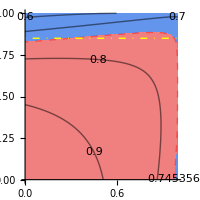

```mathematica
line=Plot[0.85,{x,0,1}, PlotStyle->{DotDashed,Thickness[Large], Yellow}];
Show[plot3,line, PlotRange->Automatic, BaseStyle -> latexStyle]
```

```mathematica
th = GetDistanceThreshold[WootersDist];
plot4 = ContourPlot[AvgDistanceOfTeleportation[ADC[pA], ADC[pB], WootersDist],{pA,0,1},{pB,0,1},
Axes -> True, Frame->False,
Contours->(Sort[Append[FindDivisions[{#1,#2},#3], th]]&),
ContourLabels->All,
ColorFunction->(p|-> If[QuantumCertified[WootersDist, p], ColorData["HTML","LightCoral"], ColorData["HTML","CornflowerBlue"]]),
ColorFunctionScaling->False,MaxRecursion->3,Mesh->None,
ImageSize -> 200, PlotLabel-> None, AxesLabel->{MaTeX["p_a"], MaTeX["p_b"]}, BaseStyle -> latexStyle
]/. Tooltip[x_,th]:>Tooltip[newStyle[x],th];
```

```mathematica
line=Plot[0.84,{x,0,1}, PlotStyle->{DotDashed,Thickness[Large], Yellow}];
Show[plot4,line, PlotRange->Automatic, BaseStyle -> latexStyle]
```